```mathematica
(* ===========================================基础函数：距离、拟合、σ、R（双向 D/σ）===========================================*)ClearAll[PointLineDistance,MeanPointToLineDistance,FitLineABCFromPts,ResidualSigma,ComputeRFromPts];

PointLineDistance[{x_,y_},{A_,B_,C_}]:=Abs[A x+B y+C]/Sqrt[A^2+B^2];

MeanPointToLineDistance[pts_List,lineABC_List]:=Mean[PointLineDistance[#,lineABC]&/@pts];

(*拟合 y=m x+b，然后转一般式 m x-y+b==0*)
FitLineABCFromPts[pts_List]:=Module[{lm,m,b,r2},lm=LinearModelFit[pts,x,x];
{m,b}=(lm["BestFitParameters"]/. Rule->List);
r2=lm["RSquared"];
<|"Model"->lm,"m"->m,"b"->b,"ABC"->{m,-1,b},"R2"->r2|>];

ResidualSigma[pts_List,lineABC_List]:=Sqrt[Mean[(PointLineDistance[#,lineABC]&/@pts)^2]];

(*计算双向 R=max(D12/σ1,D21/σ2) 或 mean 版*)
ComputeRFromPts[pts1_List,pts2_List,agg_:"Max",eps_:10^-12]:=Module[{fit1,fit2,line1,line2,d12,d21,s1,s2,r1,r2,R},fit1=FitLineABCFromPts[pts1];
fit2=FitLineABCFromPts[pts2];
line1=fit1["ABC"];line2=fit2["ABC"];
d12=MeanPointToLineDistance[pts1,line2];
d21=MeanPointToLineDistance[pts2,line1];
s1=ResidualSigma[pts1,line1];
s2=ResidualSigma[pts2,line2];
(*避免 σ=0 退化*)s1=Max[s1,eps];s2=Max[s2,eps];
r1=d12/s1;
r2=d21/s2;
R=Switch[agg,"Max",Max[r1,r2],"Mean",(r1+r2)/2,_,Max[r1,r2]];
<|"R"->R,"r1"->r1,"r2"->r2,"D12"->d12,"D21"->d21,"sigma1"->s1,"sigma2"->s2,"fit1"->fit1,"fit2"->fit2|>];


(* ===========================================基础函数：距离、拟合、σ、R（双向 D/σ）===========================================*)ClearAll[PointLineDistance,MeanPointToLineDistance,FitLineABCFromPts,ResidualSigma,ComputeRFromPts];

PointLineDistance[{x_,y_},{A_,B_,C_}]:=Abs[A x+B y+C]/Sqrt[A^2+B^2];

MeanPointToLineDistance[pts_List,lineABC_List]:=Mean[PointLineDistance[#,lineABC]&/@pts];

FitLineABCFromPts[pts_List]:=Module[{lm,m,b,r2},lm=LinearModelFit[pts,x,x];
{m,b}=(lm["BestFitParameters"]/. Rule->List);
r2=lm["RSquared"];
<|"Model"->lm,"m"->m,"b"->b,"ABC"->{m,-1,b},"R2"->r2|>];

ResidualSigma[pts_List,lineABC_List]:=Sqrt[Mean[(PointLineDistance[#,lineABC]&/@pts)^2]];

ComputeRFromPts[pts1_List,pts2_List,agg_:"Max",eps_:10^-12]:=Module[{fit1,fit2,line1,line2,d12,d21,s1,s2,r1,r2,R},fit1=FitLineABCFromPts[pts1];
fit2=FitLineABCFromPts[pts2];
line1=fit1["ABC"];line2=fit2["ABC"];
d12=MeanPointToLineDistance[pts1,line2];
d21=MeanPointToLineDistance[pts2,line1];
s1=ResidualSigma[pts1,line1];
s2=ResidualSigma[pts2,line2];
s1=Max[s1,eps];s2=Max[s2,eps];
r1=d12/s1;
r2=d21/s2;
R=Switch[agg,"Max",Max[r1,r2],"Mean",(r1+r2)/2,_,Max[r1,r2]];
<|"R"->R,"r1"->r1,"r2"->r2,"D12"->d12,"D21"->d21,"sigma1"->s1,"sigma2"->s2,"fit1"->fit1,"fit2"->fit2|>];


(* ===========================================生成线性趋势 y：y=m x+b+noise 通过选择 r2Target 来控制噪声强度，从而更容易达到 R^2>a===========================================*)

ClearAll[GenerateLinearTrendY];

GenerateLinearTrendY[x_List,mDist_,bDist_,r2Range:{r2Min_,r2Max_}]:=Module[{m,b,r2t,varX,varSignal,sigmaNoise},m=RandomVariate[mDist];
b=RandomVariate[bDist];
r2t=RandomVariate[UniformDistribution[{r2Min,r2Max}]];
varX=Variance[x];
varSignal=(m^2) varX;
(*若 x 无方差（退化），就给一个很小信号避免除0*)If[varSignal<=0,varSignal=10^-12];
sigmaNoise=Sqrt[varSignal (1-r2t)/r2t];
(m x+b)+RandomVariate[NormalDistribution[0,sigmaNoise],Length[x]]];


(* ===========================================新零模型（改版）：输入原始点集 data1,data2-固定x不变-y 生成支持两种模式：IID 或 LinearTrend-仍然保留筛选 R^2>a===========================================*)

ClearAll[GenerateNullSamplesByR2FromData];

Options[GenerateNullSamplesByR2FromData]={"A"->0.3,"NSamples"->1000,"MaxAttempts"->200000,"Aggregation"->"Max","EpsSigma"->10^-12,"Seed"->Automatic,"RequireBothPass"->True,"ReturnObserved"->True,"StoreFullSamples"->True,(*y生成模式*)"YModel"->"LinearTrend",(*"IID" 或 "LinearTrend"*)(*IID 模式：y分布*)"YDist1"->Automatic,"YDist2"->Automatic,(*LinearTrend 模式：m,b 的分布+r2目标范围*)"SlopeDist1"->Automatic,"SlopeDist2"->Automatic,"InterceptDist1"->Automatic,"InterceptDist2"->Automatic,"R2TargetMax"->0.95        (*目标R2会在[a,R2TargetMax]里抽*)};

GenerateNullSamplesByR2FromData[data1_List,data2_List,OptionsPattern[]]:=Module[{a,n,maxAtt,agg,eps,seed,reqBoth,retObs,storeFull,yModel,yd1,yd2,r2Max,sd1,sd2,id1,id2,x1,x2,y1,y2,n1,n2,fitObs1,fitObs2,mObs1,bObs1,mObs2,bObs2,sy1,sy2,distY1,distY2,distM1,distB1,distM2,distB2,attempts=0,accepted=0,pts1,pts2,fit1,fit2,Rpack,samples={},RobsPack,makePts1,makePts2},a=OptionValue["A"];
n=OptionValue["NSamples"];
maxAtt=OptionValue["MaxAttempts"];
agg=OptionValue["Aggregation"];
eps=OptionValue["EpsSigma"];
seed=OptionValue["Seed"];
reqBoth=OptionValue["RequireBothPass"];
retObs=OptionValue["ReturnObserved"];
storeFull=OptionValue["StoreFullSamples"];
yModel=OptionValue["YModel"];
yd1=OptionValue["YDist1"];
yd2=OptionValue["YDist2"];
sd1=OptionValue["SlopeDist1"];
sd2=OptionValue["SlopeDist2"];
id1=OptionValue["InterceptDist1"];
id2=OptionValue["InterceptDist2"];
r2Max=OptionValue["R2TargetMax"];
If[seed=!=Automatic,SeedRandom[seed]];
x1=data1[[All,1]];y1=data1[[All,2]];n1=Length[x1];
x2=data2[[All,1]];y2=data2[[All,2]];n2=Length[x2];
(*用原始数据拟合，作为线性趋势生成器的默认中心*)fitObs1=FitLineABCFromPts[data1];mObs1=fitObs1["m"];bObs1=fitObs1["b"];
fitObs2=FitLineABCFromPts[data2];mObs2=fitObs2["m"];bObs2=fitObs2["b"];
sy1=Replace[StandardDeviation[y1],0->1];
sy2=Replace[StandardDeviation[y2],0->1];
(*IID 分布默认：匹配原始y均值方差*)distY1=Which[yd1=!=Automatic,yd1,True,NormalDistribution[Mean[y1],sy1]];
distY2=Which[yd2=!=Automatic,yd2,True,NormalDistribution[Mean[y2],sy2]];
(*LinearTrend 的默认 m,b 分布：围绕观测值，给适度扩散*)distM1=Which[sd1=!=Automatic,sd1,True,NormalDistribution[mObs1,Max[Abs[mObs1],1]]   (*你可按需调大/调小*)];
distB1=Which[id1=!=Automatic,id1,True,NormalDistribution[bObs1,sy1]];
distM2=Which[sd2=!=Automatic,sd2,True,NormalDistribution[mObs2,Max[Abs[mObs2],1]]];
distB2=Which[id2=!=Automatic,id2,True,NormalDistribution[bObs2,sy2]];
(*两种生成器*)makePts1[]:=Module[{yy},yy=Switch[yModel,"IID",RandomVariate[distY1,n1],"LinearTrend",GenerateLinearTrendY[x1,distM1,distB1,{a,r2Max}],_,GenerateLinearTrendY[x1,distM1,distB1,{a,r2Max}]];
Transpose@{x1,yy}];
makePts2[]:=Module[{yy},yy=Switch[yModel,"IID",RandomVariate[distY2,n2],"LinearTrend",GenerateLinearTrendY[x2,distM2,distB2,{a,r2Max}],_,GenerateLinearTrendY[x2,distM2,distB2,{a,r2Max}]];
Transpose@{x2,yy}];
RobsPack=If[retObs,ComputeRFromPts[data1,data2,agg,eps],Missing["NotRequested"]];
While[accepted<n&&attempts<maxAtt,attempts++;
pts1=makePts1[];
pts2=makePts2[];
fit1=FitLineABCFromPts[pts1];
fit2=FitLineABCFromPts[pts2];
If[If[reqBoth,(fit1["R2"]>a&&fit2["R2"]>a),(fit1["R2"]>a||fit2["R2"]>a)],Rpack=ComputeRFromPts[pts1,pts2,agg,eps];
accepted++;
If[storeFull,AppendTo[samples,<|"pts1"->pts1,"pts2"->pts2,"R2_1"->fit1["R2"],"R2_2"->fit2["R2"],"fit1"->fit1["Model"],"fit2"->fit2["Model"],"line1ABC"->fit1["ABC"],"line2ABC"->fit2["ABC"],"R"->Rpack["R"],"r1"->Rpack["r1"],"r2"->Rpack["r2"],"D12"->Rpack["D12"],"D21"->Rpack["D21"],"sigma1"->Rpack["sigma1"],"sigma2"->Rpack["sigma2"]|>],AppendTo[samples,Rpack["R"]]];];];
<|"A"->a,"Aggregation"->agg,"YModel"->yModel,"R2TargetMax"->r2Max,"NSamplesRequested"->n,"NSamplesAccepted"->accepted,"Attempts"->attempts,"AcceptanceRate"->N[accepted/Max[attempts,1]],"Observed"->RobsPack,"Samples"->samples,"StoreFullSamples"->storeFull|>];


ClearAll[NullRValues];
NullRValues[result_Association]:=Module[{s=result["Samples"]},If[result["StoreFullSamples"],s[[All,"R"]],s]];
```

```mathematica
resNull=GenerateNullSamplesByR2FromData[RFPM,RFPNM,"A"->0.3,"R2TargetMax"->0.95,"YModel"->"LinearTrend","NSamples"->5000,"Seed"->1,"StoreFullSamples"->False];
Rnull=NullRValues[resNull];
Quantile[Rnull,{0.05,0.1,0.2,0.5,0.95}]
resNull["Observed"]["R"]
resNull["AcceptanceRate"]
```

{1.08659,1.20214,1.43244,2.51794,14.8655}

1.06022

0.980584

```mathematica
ClearAll[ExportNullResultsCSV];
Options[ExportNullResultsCSV]={"File"->Automatic,(*输出文件名*)"Columns"->Automatic,(*导出哪些列*)"IncludeHeader"->True       (*是否写表头*)};
ExportNullResultsCSV[resNull_Association,OptionsPattern[]]:=Module[{file,cols,includeHeader,samples,data,header},file=OptionValue["File"];
cols=OptionValue["Columns"];
includeHeader=OptionValue["IncludeHeader"];
If[file===Automatic,file=FileNameJoin[{NotebookDirectory[]/. $Failed->Directory[],"null_model_R_samples.csv"}]];
samples=resNull["Samples"];
(*情况 1：只存了 R 值（StoreFullSamples->False）*)If[VectorQ[samples,NumericQ],data=List/@N@samples;
header={"R"};
Export[file,If[includeHeader,Prepend[data,header],data],"CSV"];
Return[file];];
(*情况 2：完整样本（Association 列表）*)If[ListQ[samples]&&AssociationQ[samples[[1]]],(*默认导出列*)If[cols===Automatic,cols={"R","r1","r2","R2_1","R2_2","D12","D21","sigma1","sigma2"}];
(*只保留存在的列*)cols=Select[cols,KeyExistsQ[samples[[1]],#]&];
data=samples[[All,cols]]//Values//N;
header=cols;
Export[file,If[includeHeader,Prepend[data,header],data],"CSV"];
Return[file];];
(*兜底*)Message[ExportNullResultsCSV::invalid,"Unrecognized resNull format."];
$Failed];
```

```mathematica
ExportNullResultsCSV[resNull,"File"->FileNameJoin[{NotebookDirectory[],"SQ-trp.csv"}]];
Export[FileNameJoin[{NotebookDirectory[],"null_model_meta-SQtrp.wl"}],<|"A"->resNull["A"],"Aggregation"->resNull["Aggregation"],"YModel"->resNull["YModel"],"NSamples"->resNull["NSamplesAccepted"],"AcceptanceRate"->resNull["AcceptanceRate"],"ObservedR"->resNull["Observed"]["R"]|>];
```

```mathematica
Rnull=Import[FileNameJoin[{NotebookDirectory[],"Nullmodel","SQ-his.csv"}],"CSV"][[2;;,1]];
Robs=resNull["Observed"]["R"](*或你单独保存的*)
Quantile[Rnull,{0.05,0.5,0.95}]
```

resNull[Observed][R]

{1.06608,2.45314,13.7284}

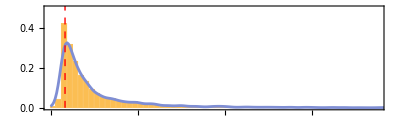

0.170166

```mathematica
Robs=1.33027;
kde=SmoothKernelDistribution[Rnull];
densMax=Max[HistogramList[Rnull,40,"PDF"][[2]]/. {}->{1}];
Nullmodelplot=Show[Histogram[Rnull,150,"PDF",ChartStyle->{RGBColor[251/255,190/255,83/255]},AspectRatio->0.3,Axes->False,Frame->True,PlotRange->{{0.0,30},{0,0.5}},FrameTicksStyle->Directive[Black,18],FrameStyle->Directive[Black,Thickness[0.0075]]],Plot[PDF[kde,x],{x,0,Max[Rnull]},PlotRange->Full,PlotStyle->RGBColor[127/255,142/255,212/255]],Graphics[{Red,Dashed,Thick,Line[{{Robs,0},{Robs,0.52}}]}]]
qHat=N@(Count[Rnull,_?(#<=Robs&)]+1)/(Length[Rnull]+1)
Export[FileNameJoin[{NotebookDirectory[],"null_model_plot-sqhis.eps"}],Nullmodelplot];
```